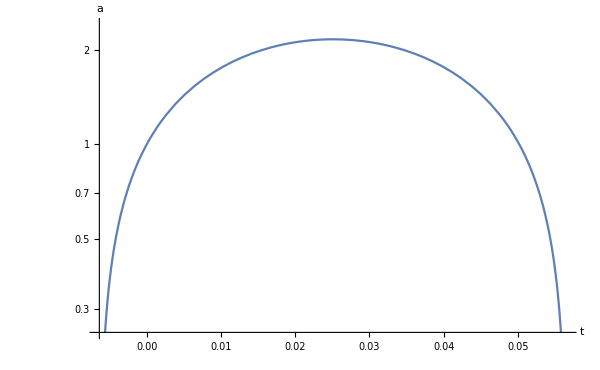
{-Graphics-,{-0.00638922,0.0565743},2.15732}

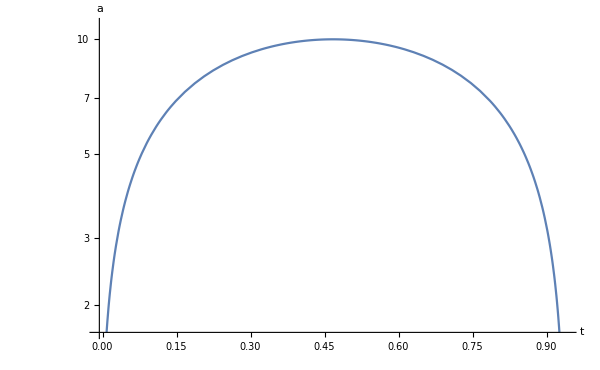
{-Graphics-,{-0.00647723,0.94077},10.0091}

```mathematica
friedmannSolve[Ω0r_, Ω0m_, Ω0Λ_, H0_, t0_, t1_] := Module[
{solution, domain},
solution = a /. NDSolve[
{
a''[t]/(a[t] H0^2) == Ω0Λ - Ω0r a[t]^(-4) - Ω0m a[t]^(-3)/2, a[0] == 1, a'[0] == H0,
WhenEvent[a[t]≤10^(-5),"StopIntegration"]
},
a, {t, t0, t1},
"ExtrapolationHandler"->{Indeterminate&,"WarningMessage"->False}
][[1]];
domain = solution["Domain"][[1]];
{
LogPlot[solution[t], {t, domain[[1]], domain[[2]]}, AxesLabel -> {t, a}, ImageSize -> 600],
domain,
Max@solution["ValuesOnGrid"]
}
]
friedmannSolve[0.01, 1.1, -0.11, 100, -0.1, 0.1]
friedmannSolve[0.01, 1.1, 0, 100, -0.1, 1]
```

```mathematica
Ω0r = 0.01;
Ω0m = 1.1;
Ω = (-a^2-a Ω0m+a^2 Ω0m-Ω0r+a^2 Ω0r)/(a^2 (-1+a^2));
a1 = {ToRules@Reduce[D[Ω, a] == 0, a]};
a101 = Select[a1, 0 < (a /. #) < 1 &]
a11∞ = Select[a1, 1 < (a /. #) &]
Ω /. a101
Ω /. a11∞
```

{{a→0.591792}}

{{a→14.9899}}

{2.73525}

{0.000163492}

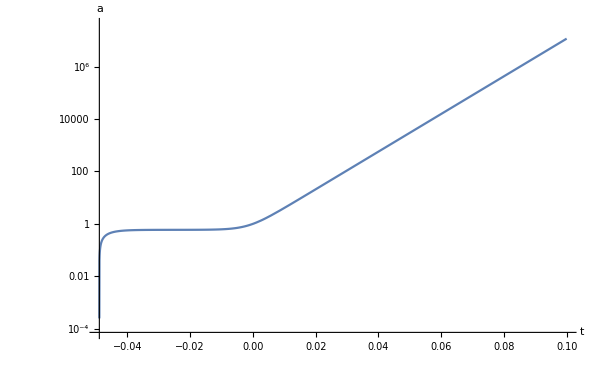
{-Graphics-,{-0.0489501,0.1},1.15876×10^7}

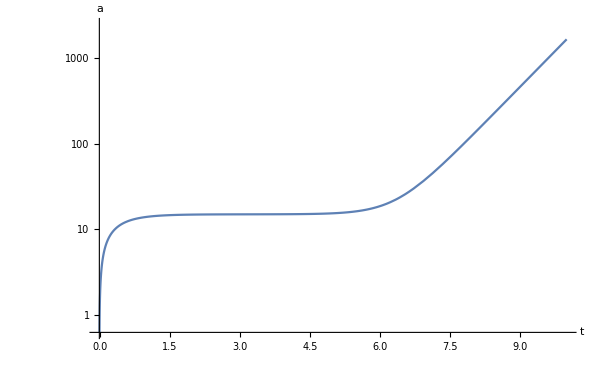
{-Graphics-,{-0.00647737,10.},1638.84}

```mathematica
friedmannSolve[0.01, 1.1,2.73524, 100, -0.1, 0.1]
friedmannSolve[0.01, 1.1,0.000163493, 100, -0.1, 10]
```

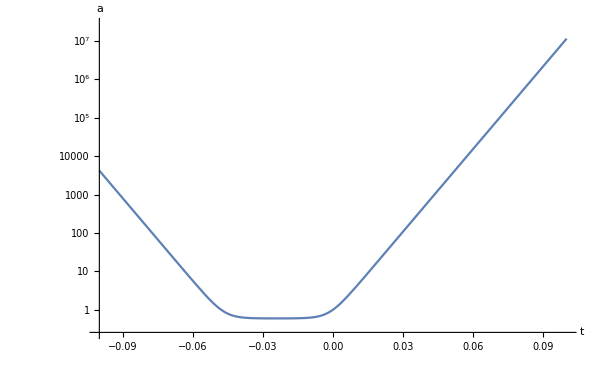
{-Graphics-,{-0.1,0.1},1.15883×10^7}

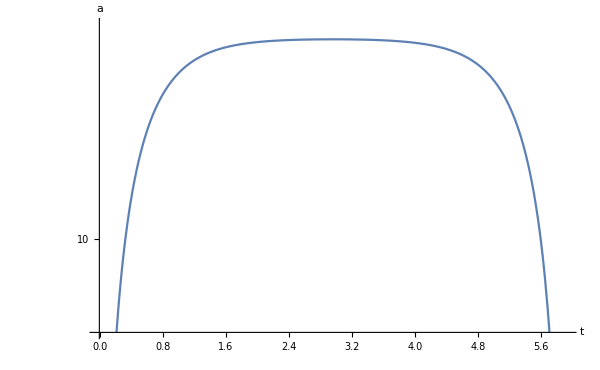
{-Graphics-,{-0.00647737,5.92069},14.9639}

```mathematica
friedmannSolve[0.01, 1.1, 2.73526, 100, -0.1, 0.1]
friedmannSolve[0.01, 1.1,0.000163491, 100, -0.1, 10]
```

```mathematica
T /.Solve[Eliminate[{ργ == 4 σ T^4/c, Ωγ == ργ/(ρc c^2), ρc == 3 H0^2/(8 π G)}, {ργ, ρc}], T] /. {
c -> Quantity["SpeedOfLight"],
H0 -> Quantity[100, "Kilometers"/"Seconds"/"Megaparsecs"],
G -> Quantity["GravitationalConstant"],
σ -> Quantity["StefanBoltzmannConstant"],
Ωγ -> Quantity[0.01, "DimensionlessUnit"]
}
UnitConvert[%]
```

{-2.36608×10^-10 c^(3/4)/(√s G^(1/4)σ^(1/4)),(0.-2.36608×10^-10 ⅈ) c^(3/4)/(√s G^(1/4)σ^(1/4)),(0.+2.36608×10^-10 ⅈ) c^(3/4)/(√s G^(1/4)σ^(1/4)),2.36608×10^-10 c^(3/4)/(√s G^(1/4)σ^(1/4))}

{-12.2222 K,(0.-12.2222 ⅈ) K,(0.+12.2222 ⅈ) K,12.2222 K}

```mathematica
nBH /.Solve[Eliminate[{Ωm == ρm/ρc, ρc == 3 H0^2/(8 π G), nBH == ρm/mBH}, {ρm, ρc}], nBH] /. {
H0 -> Quantity[100, "Kilometers"/"Seconds"/"Megaparsecs"],
G -> Quantity["GravitationalConstant"],
mBH -> Quantity[10^-10, "SolarMass"],
Ωm -> Quantity[1.1, "DimensionlessUnit"]
}
UnitConvert[%, 1/"Parsecs"^3]
```

{1.37903×10^-26 per solar massper second^2per Newtonian gravitational constant}

{3053.07 /pc^3}

```mathematica
NIntegrate[Sqrt[x^2 + y^2 + z^2], {x, y, z} ∈ Cuboid[-{1, 1, 1}/2]] Out[308]^(-1/3)
```

{0.0331078 pc}